# Linearized mBBM Notebook

Solves the eigenvalue problem associated to the linearization of the modified Benjamin-Bona-Mahony equation around a periodic (elliptic function) traveling wave. In this case the potential is taken to be 4+5 cos(x). This does not arise as the solution to BBM with any nonlinearity -- rather it is just taken to by a simple example of a periodic potential, much like the Mathieu equation. 
The code below solves the traveling wave ODE numerically, for comparison to the analytic solution.

```mathematica
Period = 2Pi;
nmodes=15;
A0=4;
A1=5;
Pot[x_] := A0 + A1 Cos[x]
Potp[x] := -A1 Sin[x]
```

Set up the matrices needed for the spectral method. We are solving , where  is the Floquet exponent or quasi-momentum. We will repeatedly solve this eigenvalue problem for different value of μ. As set up μ ranges over the interval .

```mathematica
κ=2 Pi/Period;
J[μ_]:= DiagonalMatrix[Table[I (k+μ)κ/(1+κ^2(k+μ)^2),{k,-nmodes,nmodes}]]
D1[μ_]:= DiagonalMatrix[Table[I (k+μ)κ,{k,-nmodes,nmodes}]]
P[μ_] :=  DiagonalMatrix[Table[(1+κ^2(k+μ)^2),{k,-nmodes,nmodes}]]
L[μ_] := DiagonalMatrix[Table[κ^2(k+μ)^2,{k,-nmodes,nmodes}]]

qm = Normal[SparseArray[{Band[{1,1}]->A0,Band[{1,2}]->A1/2,Band[{2,1}]->A1/2},{2nmodes+1,2nmodes+1}]];
```

```mathematica
Chop[Eigenvalues[J[0].(L[0.0]-qm)]]
```

{0.+14.6966 ⅈ,0.-14.6966 ⅈ,0.-13.6493 ⅈ,0.+13.6493 ⅈ,0.-12.6229 ⅈ,0.+12.6229 ⅈ,0.-11.5928 ⅈ,0.+11.5928 ⅈ,0.+10.5577 ⅈ,0.-10.5577 ⅈ,0.-9.51603 ⅈ,0.+9.51603 ⅈ,0.-8.46602 ⅈ,0.+8.46602 ⅈ,0.-7.40496 ⅈ,0.+7.40496 ⅈ,0.+6.32891 ⅈ,0.-6.32891 ⅈ,0.+5.23193 ⅈ,0.-5.23193 ⅈ,0.+4.10468 ⅈ,0.-4.10468 ⅈ,0.+2.93069 ⅈ,0.-2.93069 ⅈ,0.-2.14597 ⅈ,0.+2.14597 ⅈ,0.+1.66494 ⅈ,0.-1.66494 ⅈ,0.-0.136283 ⅈ,0.+0.136283 ⅈ,0}

The code below computes the eigenvalues as μ varies over .

```mathematica
evals=Flatten[Table[Chop[Eigenvalues[J[x].(L[x]-qm)]],{x,-1/2,1/2,.0005}]];
```

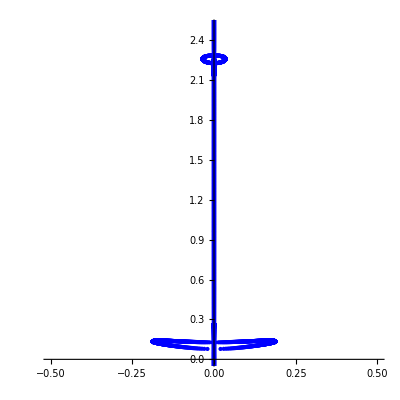

```mathematica
SFig=ComplexListPlot[evals,PlotStyle->{Blue,PointSize[Small]},PlotRange->{{-0.5,0.5},{0.0,2.5}},AspectRatio->1]
```

```mathematica
Max[Abs[Re[evals]]]
```

0.187891

```mathematica
λλ[μ_,k_] := I Chop[Eigenvalues[J[μ].(L[μ]-qm)]][[k]]
```

```mathematica
Chop[Eigenvalues[J[.2].(L[.2]-qm)]]
```

{0.+14.9002 ⅈ,0.-14.4929 ⅈ,0.+13.8541 ⅈ,0.-13.4444 ⅈ,0.+12.8284 ⅈ,0.-12.4173 ⅈ,0.+11.7992 ⅈ,0.-11.3863 ⅈ,0.+10.7652 ⅈ,0.-10.3499 ⅈ,0.+9.72495 ⅈ,0.-9.30677 ⅈ,0.+8.67681 ⅈ,0.-8.2548 ⅈ,0.+7.61822 ⅈ,0.-7.1911 ⅈ,0.+6.54556 ⅈ,0.-6.11142 ⅈ,0.+5.45338 ⅈ,0.-5.00929 ⅈ,0.+4.33318 ⅈ,0.-3.87437 ⅈ,0.+3.17056 ⅈ,0.-2.68717 ⅈ,0.+2.21466 ⅈ,0.-2.14329 ⅈ,0.+1.93587 ⅈ,0.-1.38603 ⅈ,0.+0.529716 ⅈ,-0.142561-0.139663 ⅈ,0.142561-0.139663 ⅈ}

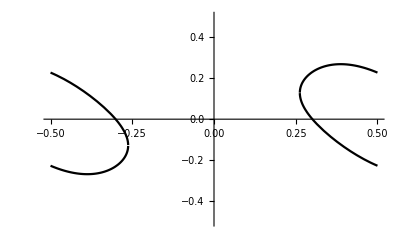

```mathematica
Bands1=Show[Plot[{λλ[x,31]},{x,-0.5,0.5},PlotRange->{{-1/2,1/2},{-0.5,0.5}},PlotStyle->Black],Plot[{λλ[x,30]},{x,-0.5,0.5},PlotRange->{{-1/2,1/2},{-0.5,0.5}},PlotStyle->Black]]
```

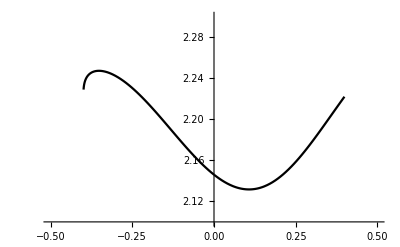

```mathematica
Bands2=Show[Plot[λλ[x,26],{x,0.0,0.399},PlotRange->{{-.5,.5},{2.1,2.3}},PlotStyle->Black],Plot[λλ[x,25],{x,-0.399,0.0},PlotRange->{{-.5,.5},{2.1,2.3}},PlotStyle->Black] ]
```

The code below solves the ODE associated with the linearized operator in order to construct the monodromy map and bifurcation index. The quantities dp[x], dq[x], dr[x] are the derivatives with respect to λ of p[x],q[x],r[x].

```mathematica
sols1=
ParametricNDSolveValue[{p'[x]== q[x],
q'[x]==r[x],
r'[x]==-λ p[x]-Potp[x] p[x] - Pot[x] q[x] + λ r[x],
dp'[x]== dq[x],
dq'[x]== dr[x],dr'[x]==-λ dp[x] - Potp[x] dp[x] - Pot[x] dq[x] + λ dr[x] -p[x] + r[x],p[0]==1,q[0]==0,r[0]==0,dp[0]==0,dq[0]==0,dr[0]==0},{p,q,r,dp,dq,dr},{x,0,25},{λ}];
sols2=
ParametricNDSolveValue[{p'[x]== q[x],
q'[x]==r[x],
r'[x]==-λ p[x]-Potp[x] p[x] - Pot[x] q[x] + λ r[x],
dp'[x]== dq[x],
dq'[x]== dr[x],dr'[x]==-λ dp[x] - Potp[x] dp[x] - Pot[x] dq[x] + λ dr[x] -p[x] + r[x],p[0]==0,q[0]==1,r[0]==0,dp[0]==0,dq[0]==0,dr[0]==0},{p,q,r,dp,dq,dr},{x,0,25},{λ}];
sols3=
ParametricNDSolveValue[{p'[x]== q[x],
q'[x]==r[x],
r'[x]==-λ p[x]-Potp[x] p[x] - Pot[x] q[x] + λ r[x],
dp'[x]== dq[x],
dq'[x]== dr[x],dr'[x]==-λ dp[x] - Potp[x] dp[x] - Pot[x] dq[x] + λ dr[x] -p[x] + r[x],p[0]==0,q[0]==0,r[0]==1,dp[0]==0,dq[0]==0,dr[0]==0},{p,q,r,dp,dq,dr},{x,0,25},{λ}];
```

```mathematica
mon[λ_?NumericQ] := {{sols1[λ][[1]][Period],sols2[λ][[1]][Period],sols3[λ][[1]][Period]},{sols1[λ][[2]][Period],sols2[λ][[2]][Period],sols3[λ][[2]][Period]},{sols1[λ][[3]][Period],sols2[λ][[3]][Period],sols3[λ][[3]][Period]}};
CharPoly[λ_?NumericQ] :=CharacteristicPolynomial[mon[λ],μ];
f[λ_?NumericQ]:=sols1[λ][[1]][Period]+sols2[λ][[2]][Period]+sols3[λ][[3]][Period]
fp[λ_?NumericQ] :=sols1[λ][[4]][Period]+sols2[λ][[5]][Period]+sols3[λ][[6]][Period]
g[λ_?NumericQ] := -1/2(Tr[mon[λ]]^2-Tr[mon[λ].mon[λ]]);
h[λ_?NumericQ] := -Conjugate[g[λ]Exp[-Period λ]];
Δ[λ_?NumericQ] := Det[mon[λ]] Exp[-Period λ];
Φ[λ_?NumericQ] := Discriminant[CharacteristicPolynomial[mon[λ],μ],μ]Exp[-2 Period λ]
Multi[λ_?NumericQ] := If[Re[Discriminant[CharacteristicPolynomial[mon[λ],μ],μ]Exp[-2 Period λ]]<0,1,I]
CP[F_,λ_] := -x^3 + F[λ] x^2 - F[-λ] Exp[Period λ/c] x + Exp[Period λ/c]
```

At the origin in the spectral plane the monodromy has three eigenvalues on the unit circle, but they are not all equal to 1. This happens for the linearization about a traveling wave due to the fact that we have a family of traveling wave solutions that generate elements of the generalized kernel of the linear operator. Since this potential does not come from a traveling wave it generally will not have this property.

```mathematica
MatrixForm[mon[0.0]]
Eigenvalues[mon[0.0]]
Abs[Eigenvalues[mon[0.0]]]
```

(-5.90546 | -0.0545988 | -0.62115
86.6226 | -0.315109 | 7.79175
62.1491 | 0.491389 | 6.59035)

{-0.315108+0.949055 ⅈ,-0.315108-0.949055 ⅈ,0.999999+0. ⅈ}

{1.,1.,0.999999}

```mathematica
CharPoly[0.0]
```

0.999999-0.369784 μ+0.369783 μ^2-μ^3

Mark the regions of higher spectral multiplicity with parallel magenta lines. (There do not appear to any intervals of multiplicity 3 in the region being plotted)

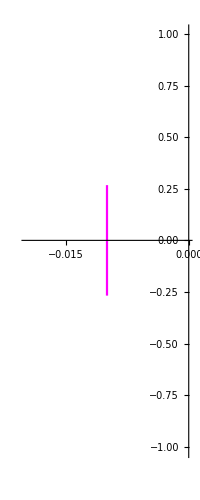

```mathematica
S1a = ParametricPlot[{.01*Multi[I x],x},{x,-3,3},PlotStyle->Magenta];
S1b = ParametricPlot[{-.01*Multi[I x],x},{x,-3,3},PlotStyle->Magenta]
```

```mathematica
Res1 = Expand[Resultant[CP[F,λ],D[CP[F,λ],λ],x]Exp[-3Period λ/c]]
Res1 /. {F[λ] -> H, F[-λ]-> Conjugate[H],F'[λ]->HP,F'[-λ]->Conjugate[HP]}
```

8 π^3-8 π^3 F[-λ] F[λ]+4 ⅇ^(2 π λ) π^2 F[-λ]^2 F'[-λ]+4 π^2 F[λ] F'[-λ]-4 ⅇ^(2 π λ) π F[-λ] F'[-λ]^2+ⅇ^(2 π λ) F'[-λ]^3+4 π^2 F[-λ] F'[λ]+4 ⅇ^(-2 π λ) π^2 F[λ]^2 F'[λ]-6 π F'[-λ] F'[λ]-2 π F[-λ] F[λ] F'[-λ] F'[λ]+F[λ] F'[-λ]^2 F'[λ]-4 ⅇ^(-2 π λ) π F[λ] F'[λ]^2+F[-λ] F'[-λ] F'[λ]^2+ⅇ^(-2 π λ) F'[λ]^3

ⅇ^(-2 π λ) HP^3-4 ⅇ^(-2 π λ) H HP^2 π+4 ⅇ^(-2 π λ) H^2 HP π^2+8 π^3+4 HP π^2 Conjugate[H]-8 H π^3 Conjugate[H]-6 HP π Conjugate[HP]+4 H π^2 Conjugate[HP]+HP^2 Conjugate[H] Conjugate[HP]-2 H HP π Conjugate[H] Conjugate[HP]+4 ⅇ^(2 π λ) π^2 Conjugate[H]^2 Conjugate[HP]+H HP Conjugate[HP]^2-4 ⅇ^(2 π λ) π Conjugate[H] Conjugate[HP]^2+ⅇ^(2 π λ) Conjugate[HP]^3

```mathematica
Bifurcation[H_,HP_,λ_] := ⅇ^(-2 π λ) HP^3-4 ⅇ^(-2 π λ) H HP^2 π+4 ⅇ^(-2 π λ) H^2 HP π^2+8 π^3+4 HP π^2 Conjugate[H]-8 H π^3 Conjugate[H]-6 HP π Conjugate[HP]+4 H π^2 Conjugate[HP]+HP^2 Conjugate[H] Conjugate[HP]-2 H HP π Conjugate[H] Conjugate[HP]+4 ⅇ^(2 π λ) π^2 Conjugate[H]^2 Conjugate[HP]+H HP Conjugate[HP]^2-4 ⅇ^(2 π λ) π Conjugate[H] Conjugate[HP]^2+ⅇ^(2 π λ) Conjugate[HP]^3
Bif2[λ_?NumericQ] := Bifurcation[f[λ],fp[λ],λ]
```

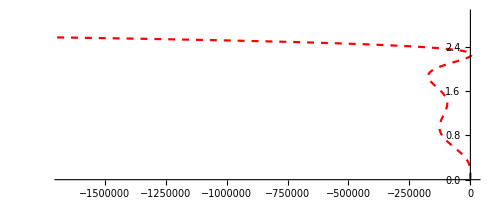

```mathematica
BifPlot=ParametricPlot[{Re[Bif2[I Z]],Z},{Z,0,3},PlotStyle->{Red,Dashed}]
```

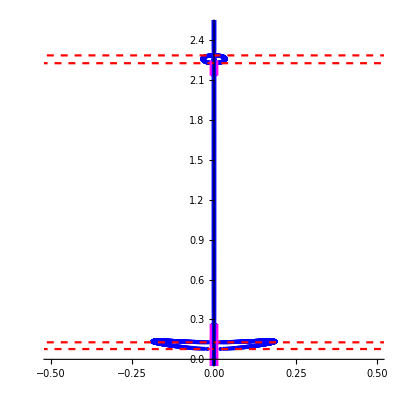

```mathematica
PaperFig=Show[SFig,BifPlot,S1a,S1b]
```

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/BBM/Figure7.png",PaperFig]
```

~/Dropbox/Jared Robby/Schmoopys/BBM/Figure7.png

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/BBM/Figure7.pdf",PaperFig]
```

~/Dropbox/Jared Robby/Schmoopys/BBM/Figure7.pdf

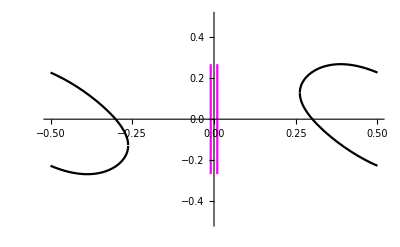

```mathematica
PaperBandFigure1 = Show[Bands1,S1a,S1b]
```

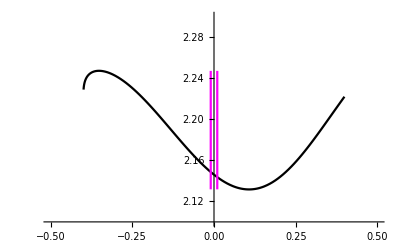

```mathematica
PaperBandFigure2 = Show[Bands2,S1a,S1b]
```

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/BBM/Figure7b.pdf",PaperBandFigure1]
```

~/Dropbox/Jared Robby/Schmoopys/BBM/Figure7b.pdf

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/BBM/Figure7c.pdf",PaperBandFigure2]
```

~/Dropbox/Jared Robby/Schmoopys/BBM/Figure7c.pdf